# UniDyn--Demo-07.nb

Aritro Sinha Roy
as836@cornell.edu
Cornell University

Abstract:  This demonstration notebook loads the UniDyn package and illustrate its use in simulating selective quantum coherence generation from two spin-1/2 particles in a multi-pulse experiment.

## Set the path to the package

Tell Mathematica the path to the directory containing the package.    

EDIT THE FOLLOWING PATH STRING:

```mathematica
$NCPath = "C:\\Users\\as836\\Documents\\GitHub";
$UniDynPath ="C:\\Users\\as836\\Documents\\GitHub\\UniDyn\\unidyn";
```

YOU SHOULD NOT NEED TO EDIT ANYTHING FROM HERE ONWARDS.

## Load the package

Append the package path to the system path.  Before trying to load the package, ask Mathematica to find it.  This is a test that we directed Mathematica to the correct directory.  The output of this command should be the full system path to the UniDyn.m file.

```mathematica
$Path = AppendTo[$Path,$NCPath];
$Path = AppendTo[$Path,$UniDynPath];
FindFile["UniDyn`"]
FindFile["NC`"]
```

C:\Users\as836\Documents\GitHub\UniDyn\unidyn\UniDyn.m

C:\Users\as836\Documents\GitHub\NC\init.m

Now that we are confident that the path is set correctly, load the package.  Setting the global $VerboseLoad variable to True will print out the help strings for key commands in the package.

```mathematica
$VerboseLoad =True; (* Set to load quietly *)
Needs["UniDyn`"]
```

NC::Directory: You are using the version of NCAlgebra which is found in: "C:\Users\as836\Documents\GitHub\NC\".

------------------------------------------------------------
NCAlgebra - Version 6.0.3
Compatible with Mathematica Version 10 and above

Authors:

  J. William Helton*
  Mauricio de Oliveira&

* Math, UCSD, La Jolla, CA
& MAE, UCSD, La Jolla, CA

with major earlier contributions by:

  Mark Stankus$ 
  Robert L. Miller#

$ Math, Cal Poly San Luis Obispo
# General Atomics Corp

Copyright: 
  Helton and de Oliveira 2023
  Helton and de Oliveira 2017
  Helton 2002
  Helton and Miller June 1991
  All rights reserved.

The program was written by the authors and by:
  David Hurst, Daniel Lamm, Orlando Merino, Robert Obar,
  Henry Pfister, Mike Walker, John Wavrik, Lois Yu,
  J. Camino, J. Griffin, J. Ovall, T. Shaheen, John Shopple. 
  The beginnings of the program come from eran@slac.
  Considerable recent help came from Igor Klep.

Current primary support is from the 
  NSF Division of Mathematical Sciences.
  
This program was written with support from 
  AFOSR, NSF, ONR, Lab for Math and Statistics at UCSD,
  UCSD Faculty Mentor Program,
  and US Department of Education.

For NCAlgebra updates see:

  www.github.com/NCAlgebra/NC
  www.math.ucsd.edu/~ncalg

------------------------------------------------------------

NCAlgebra::SmallCapSymbolsNonCommutative: All lower cap single letter symbols (e.g. a,b,c,...) were set as noncommutative.

CreateOperator::usage: CreateOperator[] is used to batch-define a bunch of operators. Example: CreateOperator[{{Ix, Iy, Iz},{Sx,Sy,Sz}}] will create six operators;  each of the operators in the first list is meant to commute with each of the operators in the second list.

CreateScalar::usage: CreateScalar[list] is used to batch-define a bunch of scalars. The parameter list can be a single scalar or a list of scalars.  Example: CreateScalar[{w1,w2}].

NCSort::usage: NCSort[list] sorts the operators in list into canonical order.

SortedMult::usage: SortedMult[list] returns Mult[list$ordered], where list$ordered are the elements of list sorted into canonical order.

MultSort::usage: MultSort[NonCommutativeMultiplyt[list]] returns returns NonCommutativeMultiply[list$ordered], where list$ordered are the elements of list sorted into canonical order.

Comm::usage: Comm[a,b] calculates the commutator of two operators.

SpinSingle$CreateOperators::usage: SpinSingle$CreateOperators[Ix,Iy,Iz,L] creates Ix, Iy, and Iz angular momentum operators and defines their commutation relations.  When the total angular momentum L = 1/2, additional rules are defined to simplify products of the angular momentum operators.  When the total angular momentum L is unspecified, no such simplification rules are defined.

OscSingle$CreateOperators::usage: OscSingle$CreateOperators[aL,aR] creates a raising operator aR and a lowering operator aL for single harmonic oscillator and defines the operator commutation relations.

Evolve::usage: Evolve[H, t, ρ] represents unitary evolution of the density operator ρ for a time t under the Hamiltonian H.  This function expands according to simplification rules but leaves the evolution unevaluated.

Evolver::usage: Evolver[H, t, ρ(0)] calculates ρ(t) = Exp[-I H t] ρ(0) Exp[+I H t], assuming that H is time independent, according to the commutation rules followed by ρ(0) and H.

## Two spin-1/2 particles: Selective quantum coherence generation

Create a  single-spin system to play with.

```mathematica
Needs["UniDyn`"];
Clear[Ix1, Iy1, Iz1,Δ1,Ix2, Iy2, Iz2,Δ2,a12,ω]
CreateScalar[{Δ1,Δ2,a12,ω}];
CreateOperator[{{Ix1, Iy1, Iz1},{Ix2,Iy2,Iz2}}];
SpinSingle$CreateOperators[Ix1, Iy1, Iz1,1/2];
SpinSingle$CreateOperators[Ix2, Iy2, Iz2,1/2];
```

SpinSingle$CreateOperators::nocreate: Spin operators already exist.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::simplify: Angular momentum L = 1/2. Adding operator simplification rules.

SpinSingle$CreateOperators::nocreate: Spin operators already exist.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::simplify: Angular momentum L = 1/2. Adding operator simplification rules.

```mathematica
SimplifyingEvolver[H_,t_,ρ$0_]:=  

(*   H = Hamiltonian operator *)
(*   t = time varaible *)
(* ρ$0 = initial density operator *)

Evolver[H, t, ρ$0]//Simplify// ExpToTrig
```

Define free-evolution and pulse propagators

```mathematica
(* Extraction of operators from an expression *)
op$extA[elem_]:=Module[{pos,ans},
pos=Position[NonCommutativeQ/@Level[elem,1],True];
ans=Level[elem,1][[pos[[1,1]]]];
Return[ans];
]

op$ext[elem_]:=Module[{ans},
If[Dimensions[elem]==={},ans = elem,
ans = Check[op$extA[elem],If[NonCommutativeQ@elem,elem,None]]//Quiet];
Return[ans];
]
```

```mathematica
(* Group and simplify expressions by operators *)
col$op[exp_,op_,s_]:= Module[{op$l,exp$l,dim,exp$s,j},exp$l = exp//Expand;dim = Dimensions[exp$l][[1]];op$l = {};For[j=1,j≤dim,j++,op$l = Append[op$l,op$ext[exp$l[[j]]]]];op$l = DeleteDuplicates[op$l];If[op==1,exp$s = Simplify[#,TimeConstraint->s]&/@Collect[exp$l,op$l],If[op==2,exp$s = FullSimplify[#,TimeConstraint->s]&/@Collect[exp$l,op$l],exp$s = Collect[exp$l,op$l]]];Return[exp$s]]
```

```mathematica
(* Define free-evolution under the influence of the secular spin Hamiltonian *)
FreeEvolution[ρ_,t_, sim_]:=(*ρ=density operator*)(*t=time[s]*)(* sim = 1: Simplify, 2: FullSimplify *)
Module[{dim, A, B, Anew,ρnew},
dim = Dimensions[ρ][[1]];
ρnew = 0;
For[j=1,j<=dim,j++,
A = op$ext[ρ[[j]]];
B = ρ[[j]]/A;
Anew = ((A//SimplifyingEvolver[Δ1 Iz1,t,#]&//SimplifyingEvolver[Δ2 Iz2,t,#]&//SimplifyingEvolver[a12 Iz1**Iz2,t,#]&)//NCExpand//MultSort)//NCExpand;
AddTo[ρnew,B Anew];
];
ρnew= col$op[ρnew,sim,1]; (* Timeconstraint = 1 for simplification *)
Return[ρnew];
]
```

```mathematica
(* Define ideal δ-pulses with flip angle θ and phase ϕ *)
Pulse[ρ_,θ_,ϕ_,sim_]:=(*ρ=density operator*)(*θ=flip angle*)(*ϕ=phase*)
 Module[{dim, A, B, Anew,ρnew},
ρnew = 0;
If[Dimensions[ρ]=={},
Anew = ((ρ//SimplifyingEvolver[Ix1 Cos[ϕ],θ,#]&//SimplifyingEvolver[Ix2 Cos[ϕ],θ,#]&//SimplifyingEvolver[Iy1 Sin[ϕ],θ,#]&//SimplifyingEvolver[Iy2 Sin[ϕ],θ,#]&)//NCExpand//MultSort)//NCExpand;
AddTo[ρnew,Anew],
dim = Dimensions[ρ][[1]];
For[j=1,j<=dim,j++,
A = op$ext[ρ[[j]]];
B = ρ[[j]]/A;
(* Anew =Evolver[(Iy1+Iy2)*Sin[ϕ],θ,Evolver[(Ix1+Ix2)*Cos[ϕ],θ,A]//MultSort]//MultSort//NCExpand; *)
 
Anew = ((A//SimplifyingEvolver[Ix1 Cos[ϕ],θ,#]&//SimplifyingEvolver[Ix2 Cos[ϕ],θ,#]&//SimplifyingEvolver[Iy1 Sin[ϕ],θ,#]&//SimplifyingEvolver[Iy2 Sin[ϕ],θ,#]&)//NCExpand//MultSort)//NCExpand;
;

AddTo[ρnew,B*Anew];
]]//Quiet;
ρnew= col$op[ρnew,sim,1]; (* Timeconstraint = 1 for simplification *)
Return[ρnew];
]
```

Overview of the pulse-sequence

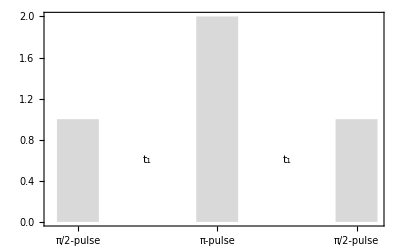

```mathematica
text$1 = Text[Style["t_1",Large],{2.5,0.6}];
text$2 = Text[Style["t_1",Large],{5.5,0.6}];
gr$ = Graphics[{text$1,text$2}];
pp$ = BarChart[{1,Missing[],Missing[],2,Missing[],Missing[],1},ChartStyle->{"Pastel",LightGray},ChartBaseStyle->EdgeForm[None],
ChartLabels->{"π/2-pulse","","","π-pulse","","","π/2-pulse"},LabelStyle->{FontSize->22},
Frame->{True,True,False,False},FrameTicksStyle->{Opacity[0],Opacity[1]},FrameStyle->Opacity[0],
(* Axes->{True,False},*) ImageSize->400];
DeleteCases[pp$,_Line?(Not@*FreeQ[_Offset]),All];
Show[pp$,gr$]
```

Density operator evolution

```mathematica
(* Subscript[ρ, 0] is the density operator at thermal equilibrium *)
ρ0 = Iz1+Iz2; 
(* Application of the first π/2-pulse with its phase set to {0, π/2, π, 3 π/2} *)
Quiet[
ρ1A = Pulse[ρ0,π/2,0,2];
ρ1B = Pulse[ρ0,π/2,π/2,2];
ρ1C = Pulse[ρ0,π/2,π,2];
ρ1D = Pulse[ρ0,π/2,3*π/2,2];
]
```

```mathematica
(* A free-evolution period *)
Quiet[
ρ2A = FreeEvolution[ρ1A,t1,2];
{{ρ2B = FreeEvolution[ρ1B,t1,2];}, {ρ2C = FreeEvolution[ρ1C,t1,2];
ρ2D = FreeEvolution[ρ1D,t1,2];}}
]
```

```mathematica
(* Application of the first refocusing π-pulse with its phase set to {0, π/2, π, 3 π/2} *)
ρ3A = Pulse[ρ2A,π,0,1];
ρ3B = Pulse[ρ2B,π,π/2,1];
ρ3C = Pulse[ρ2C,π,π,1];
ρ3D = Pulse[ρ2D,π,3*π/2,1];
```

```mathematica
(* The second free-evolution period *)
ρ4A = FreeEvolution[ρ3A,t1,1];
ρ4B = FreeEvolution[ρ3B,t1,1];
ρ4C = FreeEvolution[ρ3C,t1,1];
ρ4D = FreeEvolution[ρ3D,t1,1];
```

Selective excitation of even-order coherences by in sync pulse phasing ϕ_1=ϕ_2=ϕ_3

```mathematica
ρ5A = Pulse[ρ4A,π/2,0,1];
ρ5B = Pulse[ρ4B,π/2,π/2,1];
ρ5C = Pulse[ρ4C,π/2,π,1];
ρ5D = Pulse[ρ4D,π/2,3*π/2,1];
```

```mathematica
(* Zero quantum coherence selection *)
ρ5$ZQ = 1/4*(ρ5A+ρ5B+ρ5C+ρ5D)//Expand
```

Iz1 Cos[a12 t1]+Iz2 Cos[a12 t1]

```mathematica
(* Double quantum coherence selection *)
ρ5$DQ = 1/4*(ρ5A-ρ5B+ρ5C-ρ5D)//Expand
```

2 Ix1**Iy2 Sin[a12 t1]+2 Iy1**Ix2 Sin[a12 t1]

Selective excitation of odd-order coherences by offsetting the phase of the second π/2-pulse; ϕ_1=ϕ_2, ϕ_3=ϕ_1+π/2

```mathematica
ρ5W = Pulse[ρ4A,π/2,π/2,1];
ρ5X = Pulse[ρ4B,π/2,π,1];
ρ5Y = Pulse[ρ4C,π/2,3*π/2,1];
ρ5Z = Pulse[ρ4D,π/2,2*π,1];
```

```mathematica
(* Single quantum coherence selection *)
ρ5$SQ = 1/4*(ρ5W-ⅈ*ρ5X-ρ5Y+ⅈ*ρ5Z)//Expand
```

1/2 ⅈ Ix1 Cos[a12 t1]+1/2 ⅈ Ix2 Cos[a12 t1]+1/2 Iy1 Cos[a12 t1]+1/2 Iy2 Cos[a12 t1]+Ix1**Iz2 Sin[a12 t1]-ⅈ Iy1**Iz2 Sin[a12 t1]+Iz1**Ix2 Sin[a12 t1]-ⅈ Iz1**Iy2 Sin[a12 t1]